As a aspiring fitness trainer it is my task to create training plans. When I attended a workshop called yoga in sport science, the tutor, which was a young golf teacher, created training plans in an excel sheet. Seeing that I thought there has to be a better way.
Today I want to demonstrate you how to create nice looking plans individually adapted with tons of possibilities from which I can show only a small excerpt, but still it will be for many too much too grasp, lets see.

There are two possibilities, for those who want to search for information just head over to [WolframAlpha](www.wolframalpha.com) and type yoga or pilates in the search field and will be welcomed with plenty of search examples, try them all out.
WolframAlpha is, unlike google, a semantic search engine which searches for information instead of links.

There is also a nifty overview [Health & Medicine]( www.wolframalpha.com/examples/science-and-technology/health-and-medicine/) site with examples for weight loss computations, heart rate calculators, body statistics, medical tests and computations, anatomy and so on. One can easily spend days there just to explore the possibilities.

For the adventurous ones of us, we dive even deeper and access the vast amount of information programmatically. If you want to follow along head over to the [Wolfram Cloud](https://develop.open.wolframcloud.com/app/), to access the Wolfram System notebook, an interactive interface for simple calculations to full publishable documents and sophisticated dynamic interfaces. If you want to save your changes you can further sign in, the free access has enough features for our needs. 

I will limit this tutorial to the YogaPose class, but you can as well check out the PilatesExercise class which has :

```mathematica
Length[EntityList["PilatesExercise"]]
```

53

exercise entities, which are more strength oriented like push ups and one leg kicks.

Now lets dive into the possibilities we have, the most obvious, the yoga poses:

```mathematica
EntityList["YogaPose"]
```

{Accomplished Pose,Ananta's Pose,Anjaneya's Pose,Archer Pose,Auspicious Pose,Balancing Half Moon Pose,Balancing Table Pose,Basic One-Legged King Pigeon Pose,Bharadvaja's Pose,Big Toe Pose,Bikram Triangle Pose,195,Upward Facing Dog Pose,Upward Facing Seated Forward Bend Pose,Upward Lotus Pose,Upward Plank Pose,Warrior III Pose,Warrior II Pose,Warrior I Pose,Wild Thing Pose,Wind Relieving Pose,Yoga Sleep Pose}
 |  |  |  |

Plenty to begin with, lets see how many we have, the % sign means use the last result:

```mathematica
Length[%]
```

216

Quite manageable i would say, lets see what else there is, how are they grouped?

```mathematica
EntityClassList["YogaPose"]
```

{arm balancing yoga poses,head standing yoga poses,kneeling yoga poses,one-legged balancing yoga poses,prone yoga poses,quadruped yoga poses,reclining yoga poses,seated yoga poses,shoulder standing yoga poses,standing yoga poses,back bend yoga poses,forward bend yoga poses,postural yoga poses,side bend yoga poses,twist yoga poses,inverted yoga poses,beginner yoga poses,advanced yoga poses,intermediate yoga poses,medium intensity yoga poses,high intensity yoga poses,low intensity yoga poses,yoga poses to improve balance,yoga poses to improve mobility in abdomen,yoga poses to improve mobility in ankles,yoga poses to improve mobility in arms,yoga poses to improve mobility in back,yoga poses to improve mobility in chest,yoga poses to improve mobility in feet,yoga poses to improve mobility in hip joints,yoga poses to improve mobility in legs,yoga poses to improve mobility in neck,yoga poses to improve mobility in knees,yoga poses to improve mobility in buttocks,yoga poses to improve mobility in shoulders,yoga poses to improve mobility in thoracic vertebral column,yoga poses to improve mobility in vertebral column,yoga poses to improve mobility in wrists,yoga poses to improve posture,yoga poses to improve strength in abdomen,yoga poses to improve strength in ankles,yoga poses to improve strength in arms,yoga poses to improve strength in back,yoga poses to improve strength in chest,yoga poses to improve strength in feet,yoga poses to improve strength in hands,yoga poses to improve strength in hip joints,yoga poses to improve strength in legs,yoga poses to improve strength in knees,yoga poses to improve strength in neck,yoga poses to improve strength in buttocks,yoga poses to improve strength in shoulders,yoga poses to improve strength in wrists,yoga poses to strengthen calves,yoga poses to strengthen deep rotators of hip,yoga poses to strengthen groin,yoga poses to strengthen hamstrings,yoga poses to strengthen hip flexors,yoga poses to strengthen iliopsoas,yoga poses to strengthen pectoral muscles,yoga poses to strengthen piriformis,yoga poses to strengthen quads,yoga poses to strengthen rotator cuff,yoga poses to stretch calves,yoga poses to stretch deep rotators of hip,yoga poses to stretch groin,yoga poses to stretch hamstrings,yoga poses to stretch hip flexors,yoga poses to stretch iliopsoas,yoga poses to stretch pectoralis minor,yoga poses to stretch pectoral muscles,yoga poses to stretch piriformis,yoga poses to stretch hamstrings,yoga poses to stretch rotator cuff}

```mathematica
Length[%]
```

74

With that many categories there should be enough for every use case. But wait, there is more, we got various positions,

```mathematica
EntityList["YogaPosition"]
```

{arm balancing,back bend,chin standing,forward bend,head standing,kneeling,one-legged balancing,postural,prone,quadruped,reclining,seated,shoulder standing,side bend,standing,twist}

properties ranging from Sanskrit names, props to use, counter poses, to which muscles are stretched or strengthened,

```mathematica
EntityProperties["YogaPose"]
```

{alternate names,popular curve,associated species,asymmetrical,body position,contraindications,counter poses,description,experience level,intensity level,inverted,joint motion,name,potential benefits,precautions,preparatory poses,primary contracted muscles,props,Sanskrit transliteration,schematic,simplified schematic,sites of improved function,sites of improved mobility,sites of improved strength,sites of recent surgery, injury, or inflammation,sites of weakness, stiffness, or sensitivity,spine position,stretched muscles,supporting muscles,typical sequences,variations}

we can work with different sequences like the ashtanga primary or secondary series or the jivamukti spiritual warrior sequence,

```mathematica
EntityList["YogaSequence"]
```

{Ashtanga Backbend Beginner,Ashtanga Backbend Intermediate,Ashtanga Closing Sequence,Ashtanga Primary Part 1,Ashtanga Primary Part 2,Ashtanga Primary Part 3,Ashtanga Primary Part 4,Ashtanga Primary Series,Ashtanga Second Part 1,Ashtanga Second Part 2,Ashtanga Second Part 3,Ashtanga Second Part 4,Ashtanga Second Series,Ashtanga Seven Headstands,Ashtanga Standing Sequence,Basic Sun Salutation,Bikram Twenty-six,Jivamukti Spiritual Warrior,Jivamukti Magic Ten,Jivamukti Sun Salutation A,Jump Back Vinyasa,Jump Through Vinyasa,Sivananda Twelve Basic Postures,Sun Salutation A,Sun Salutation B,Vinyasa}

## Example 1

Lets say my client wants wants to do just a few poses, which simultaneously strengthen their bootie, so obviously a female, strengthen her back, improve the mobility in her legs and strengthen her knees.

The orange boxes you see next are created through inline free-form input	fields which you can access with Ctrl+=.

You can then use free form linguistics to create the classes, like shown in bold, for example if you type "yoga poses to improve strength in back" and hit enter, you get the entity class EntityClass["YogaPose", "YogaPosesToImproveStrengthInBack"]. You can see the full class if you hover over them.

First we create 4 variables and store the poses of the different categories in it:

```mathematica
butt=EntityList[EntityClass["YogaPose","YogaPosesToImproveStrengthInButtocks"]];
back=EntityList[EntityClass["YogaPose","YogaPosesToImproveStrengthInBack"] ];
legs =EntityList[EntityClass["YogaPose","YogaPosesToImproveMobilityInLegs"]];
knees = EntityList[EntityClass["YogaPose","YogaPosesToImproveStrengthInKnees"]];
```

The Intersection command , which can also be typed as ∩ with ESC inter ESC, returns only the poses occurring in all 4 categories. 
If you see somewhere a variable in blue color it means that it is not evaluated yet, so head over to that cell and hit shift+enter.

```mathematica
finalplan=Intersection[butt, back, legs, knees]
```

{Goddess Pose,Lord of the Dance Pose,Warrior III Pose}

There are just 3 poses matching all categories, lets see how they look like. 
The GraphicsRow command shows them without coma separated  list in parenthesis, when you want to copy the cell as image.

```mathematica
graph=GraphicsRow[EntityValue[finalplan,"SimplifiedSchematic"]]
```

-Graphics-

Maybe you don't like the color, how about pink?

```mathematica
pink=graph /.RGBColor[___]->Pink
```

-Graphics-

You can resize them,

```mathematica
Show[pink,ImageSize ->Medium]
```

-Graphics-

or maybe you prefer the detailed schematics

```mathematica
EntityValue[finalplan,"Schematic"]
```

{-Graphics-,-Graphics-,-Graphics-}

## Example 2

You want to do poses which strengthen the most muscles at a time. The Property we need for that is called "sites of improved strength" in natural language. Because we work with properties instead of classes, we need to associate the poses with the muscles which will be strengthened. As we see in the shortened associative array below, the wind relieving pose is not in the group of poses that make you strong.

```mathematica
ev=EntityValue["YogaPose", 
  EntityProperty["YogaPose", "SitesOfImprovedStrength"], "EntityAssociation"]
```

Accomplished Pose→{back,abdomen},Ananta's Pose→{abdomen,back,hand,shoulder,leg},212,Wind Relieving Pose→Missing[NotAvailable],Yoga Sleep Pose→{abdomen,back,leg}
 |  |  |  |

Next we look how many entities we have that strengthen the most muscles in a nifty histogram:

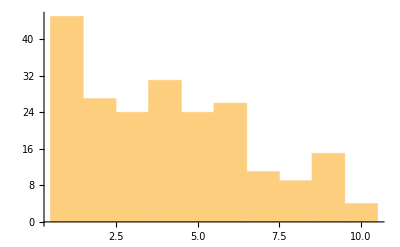

```mathematica
Histogram[Length /@ ev]
```

There are 4 poses which strengthen 10 muscles at the same time, lets see which ones.
We sort the list by the number of muscles involved, and give the -4 parameter to the Take command, which shows us the last 4 entries.

```mathematica
strength=Keys[Take[SortBy[ev, Length], -4]]
```

{Extended Hand to Big Toe Pose B,Fire Hydrant Pose,Side Plank Pose,Warrior III Pose}

Lets pay a little respect to ancient India and get some Sanskrit names. I spared you the Devanagari script because the half letters are not joined. Fire hydrant pose has no name because there weren’t fire hydrants in ancient India, so i had to delete the Missing entry and  with the warrior III pose obviously not only human struggle, but the Keys command too, claiming that it is not a valid list of rules. The two names for this pose are vīrabhadrāsanaIII and digāsana.

```mathematica
sans=DeleteMissing[EntityValue[strength,"SanskritTransliteration"]]
Keys[sans[[{1,2}]]]
{{"utthita hasta pādāṅguṣṭhāsana B","utthita pārśvasahita"},{"vasiṣṭhāsana"}}
```

And here they are:

```mathematica
GraphicsRow[EntityValue[strength,EntityProperty["YogaPose", "SimplifiedSchematic"]] ,ImageSize ->Large]
```

-Graphics-

I hope I could give you a small glimpse of what is possible with the wolfram development platform, only the sky is the limit and your imagination is the limit.
Until next time,
Miron